```mathematica
(* Text like this one that are between parentheses and asterisks  are nonexecutable comments. *)
(* Import the data using the file path, which can be done through the "Insert" tab, followed by the "File Path" option. Find the file to import, which will add the path. Place the File Path in the Import command, between the brackets and quotation marks. Hit shift+enter to execute the command. *)
Import["/Users/tstack/Desktop/kinetics.csv"]//TableForm
```

[Sub] | v/E
2.4 | 0.770713
3.75 | 0.963391
6 | 1.15607
9 | 2.11946
15 | 2.60116
24 | 3.66089
37.5 | 5.68401
60 | 4.91329
2.4 | 0.770713
3.75 | 0.770713
6 | 1.15607
9 | 1.83044
15 | 2.89017
24 | 4.14258
37.5 | 5.97303
60 | 5.97303
2.4 | 0.578035
3.75 | 0.963391
6 | 1.25241
9 | 1.63776
15 | 2.79383
24 | 4.72062
37.5 | 4.81696
60 | 5.29865
[Sub] | avg v/E
2.4 | 0.706487
3.75 | 0.899165
6 | 1.18818
9 | 1.86256
15 | 2.76172
24 | 4.17469
37.5 | 5.49133
60 | 5.39499

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{kcat→8.74556,ksp→0.294779}, | Estimate | Standard Error | t-Statistic | P-Value
kcat | 8.74556 | 1.11101 | 7.8717 | 0.000222538
ksp | 0.294779 | 0.0416145 | 7.08357 | 0.000397047}

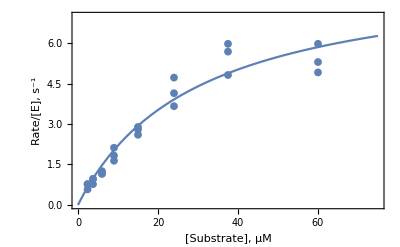

```mathematica
(* Select the rows for the average data and copy/paste to define that data sets (repeating for the full data). Adding semicolons after the end of the commands does not show the output. Before a data set is defined they will begin in blue font and change to black once executed. Mathematica includes small "`" symbols to indicate that there are more numbers than shown on screen.*)
avgData={{2.4, 0.7064868}, {3.75, 0.8991651}, {6, 1.1881824}, {9, 1.8625562}, {15, 2.7617213}, {24, 4.1746949}, {37.5, 5.4913295}, {60, 5.3949904}};
fullData={{2.4, 0.7707129}, {3.75, 0.9633911}, {6, 1.1560694}, {9, 2.1194605}, {15, 2.6011561}, {24, 3.6608863}, {37.5, 5.6840077}, {60, 4.9132948}, {2.4, 0.7707129}, {3.75, 0.7707129}, {6, 1.1560694}, {9, 1.8304432}, {15, 2.8901734}, {24, 4.1425819}, {37.5, 5.973025}, {60, 5.973025}, {2.4, 0.5780347}, {3.75, 0.9633911}, {6, 1.2524085}, {9, 1.6377649}, {15, 2.7938343}, {24, 4.7206166}, {37.5, 4.8169557}, {60, 5.2986513}};
(* Define the nonlinear modified Michaelis Menten equation used in the data fitting. Check again that once executed the "ModifiedMM" turns from blue to black in color,while the substrate concentration "S" and the kinetic constants remain blue (as these are the variables). Then fit the data to the equation and report the parameters as estimates and includes the standard error.*)
ModifiedMM=(ksp*S)/(1+(ksp*S)/(kcat));
Model=NonlinearModelFit[avgData,{ModifiedMM,kcat>0,ksp>0},{kcat,ksp},S];
Model[{"BestFitParameters","ParameterTable"}]
(* Create plot of the data. Change the PlotRange {{Subscript[x, min], Subscript[x, max]},{Subscript[y, min], Subscript[y, max]}} to properly frame your data as needed. Change the FrameLabel title to match the name of the substrate. *)
(* Save the output Plot by right clicking the image and select "Save Graphic As..." *)
Show[ListPlot[{fullData},PlotRange->{{0,75},{0,7}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],Plot[{Model[S]},{S,0,75}],LabelStyle->Directive[Bold,Medium]]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{kcat→8.74556,ksp→0.294779}, | Estimate | Standard Error | t-Statistic | P-Value
kcat | 8.74556 | 1.11101 | 7.8717 | 0.000222538
ksp | 0.294779 | 0.0416145 | 7.08357 | 0.000397047}

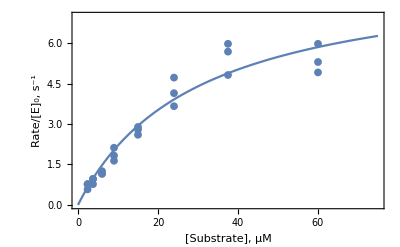

```mathematica
(* The NonLinearModelFit includes limits to Subscript[k, cat] and Subscript[k, SP], indicating that they need to be greater than 0. If these bounds alone do not provide a good fit, add to or change these bounds so the model finds the true best fit. Recall that Subscript[k, cat] indicates the upper limit of the velocity, and that Subscript[k, SP] represent the initial linear portion of the curve. The command below demonstrates how to change the upper and lower bounds of the variables. *)
(*Sometimes Mathematica has difficulty drawing the full curve from 0 to the final value so plotting the curve twice with two different ranges can circumvent this issue.*)
Model=NonlinearModelFit[avgData,{ModifiedMM,kcat>4,kcat<20,ksp>0.01,ksp<5},{kcat,ksp},S];
Model[{"BestFitParameters","ParameterTable"}]
Show[ListPlot[{fullData},PlotRange->{{0,75},{0,7}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E]_0, s^-1"}],Plot[{Model[S]},{S,0,10}],Plot[{Model[S]},{S,10,75}],LabelStyle->Directive[Bold,Medium]]
```

```mathematica
(* The calculations below are to demonstrate how to report the kinetic constants. The first calculation determines Subscript[K, m]. *)
(*Subscript[K, m] of modified method = Subscript[k, cat]/Subscript[k, sp]*)
8.74556018809328/(0.2947793892422576)(* The next two calculate the error of Subscript[K, m]. *)
(*error/Subscript[K, m] of modified method using error propagation=[(error Subscript[k, cat](/Subscript[k, cat]))^2+(error Subscript[k, sp](/Subscript[k, sp]))^2]^0.5*)
((1.1110132625333868/8.74556018809328)^2+(0.041614539570106086/0.2947793892422576)^2)^(0.5)
(* Note that Subscript[k, sp](Subscript[k, cat]/Subscript[K, m]) has units dependent on the data. For the provided data,the substrate concentration has units of μM, the rate has units of s^-1. As fit,the Subscript[k, sp] constant has units of μM^-1 s^-1 which should be converted to 
M^-1s^-1. *)
(* Subscript[k, sp] conversion from μM^-1 s^-1 to M^-1 s^-1 *)
0.2947793892422576*10^6
(* Subscript[k, sp] error conversionfrom μM^-1 s^-1 to M^-1 s^-1*)
0.041614539570106086*10^6
(* The kinetic values are reported as:
  Subscript[k, cat] = 9 ± 1 s^-1
Subscript[K, m] = 30. ± 6 μM
Subscript[k, sp] = 2.9 ± 0.4 × 10^5 M^-1 s^-1 *)
(* A great dataset has less than 10% error and this is pretty close. A good data set is 15 to 20% error. Better data could potentially be achieved by using the estimated value of Subscript[K, m]to determine the range of concentrations to test as described in the main text. *)
```

29.6682

0.189916

294779.

41614.5

{{1.02342,0.0906551}, | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.02342 | 0.418963 | 2.44274 | 0.0502839
S | 0.0906551 | 0.0153702 | 5.89811 | 0.00105503}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{kcat→6.72225,kspH→115.845,n→1.38322}, | Estimate | Standard Error | t-Statistic | P-Value
kcat | 6.72225 | 0.935269 | 7.18751 | 0.000811538
kspH | 115.845 | 46.5771 | 2.48717 | 0.0553525
n | 1.38322 | 0.268511 | 5.15145 | 0.00361051}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{kcat→16.0648,ksp→999.999,KI→72.6805}, | Estimate | Standard Error | t-Statistic | P-Value
kcat | 16.0648 | 11.6662 | 1.37705 | 0.226955
ksp | 999.999 | 1601.62 | 0.624368 | 0.559766
KI | 72.6805 | 108.329 | 0.670924 | 0.532009}

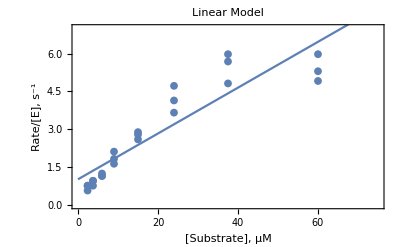

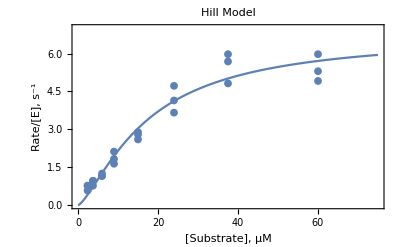

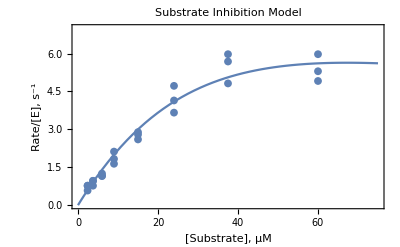

```mathematica
(* Below are alternative equations to use in fitting enzyme data. *)
Hill=(kcat*(S^n))/((kspH/kcat)^n+S^n);
SubInh=(kcat*(S))/((ksp/kcat)+S(1+S/KI));
(* If saturating levels of substrate are not reached, the data will be best fit by a straight line. In that case, the slope of the line provides the value of and Subscript[k, SP], but does not determine estimates Subscript[k, cat] or Subscript[K, m] in this case. The slope is provided by the "S" estimate*) 
LinearModel=LinearModelFit[avgData,S,S];
LinearModel[{"BestFitParameters","ParameterTable"}]
HillModel=NonlinearModelFit[avgData,{Hill, kcat>0,kspH>0,n>0},{kcat,kspH,n},S];
HillModel[{"BestFitParameters","ParameterTable"}]
SubInhModel=NonlinearModelFit[avgData,{SubInh, kcat>0,ksp>0,KI>0,kcat<100,ksp<1000},{kcat,ksp,KI},S];
SubInhModel[{"BestFitParameters","ParameterTable"}]
Show[ListPlot[{fullData},PlotRange->{{0,75},{0,7}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],Plot[{LinearModel[S]},{S,0,75}],LabelStyle->Directive[Bold,12],PlotLabel->"Linear Model"]
Show[ListPlot[{fullData},PlotRange->{{0,75},{0,7}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],Plot[{HillModel[S]},{S,0,75}],LabelStyle->Directive[Bold,12],PlotLabel->"Hill Model"]
Show[ListPlot[{fullData},PlotRange->{{0,75},{0,7}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],Plot[{SubInhModel[S]},{S,0,75}],LabelStyle->Directive[Bold,12],PlotLabel->"Substrate Inhibition Model"]
```